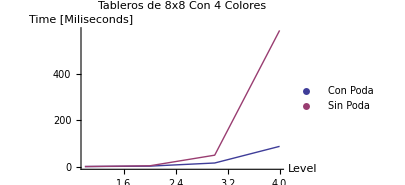
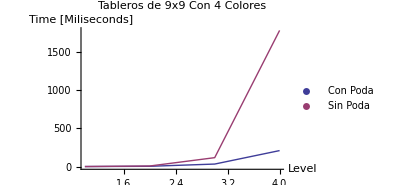
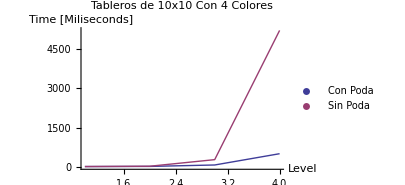
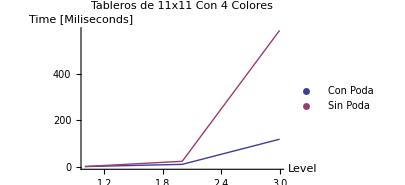
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
s = Import["C:\\Users\\Lucas\\Desktop\\data.txt","Table"];
j=4;
smatrix = Table[ Cases[s,{a_,b_,c_,d_,e_,g_}/; a==b==i && c ==j],{i,8,11}];
plots = Table[ListPlot[{Transpose[{smatrix[[i]][[All,4]],smatrix[[i]][[All,5]]}],Transpose[{smatrix[[i]][[All,4]],smatrix[[i]][[All,6]]}]},Joined->True,PlotRange->{All,All},PlotLegends->{"Con Poda","Sin Poda"},AxesLabel->{"Level","Time [Miliseconds]"},AxesOrigin->{0,0},PlotLabel->"Tableros de "<>ToString[i+7]<>"x"<>ToString[i+7 ]<>" Con "<>ToString[j]<>" Colores",ImageSize->{300,300}  ],{i,1,4}];

t1 = Grid[Partition[plots,2],Frame->All,Alignment->{Center,Center},Spacings->{0,0}]
Export["Tabla de colores "<>ToString[j-1]<>".jpg",t1,"JPG",ImageResolution->300];
```